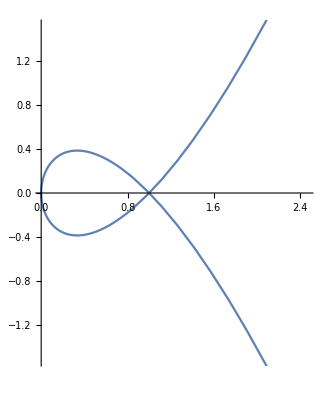

```mathematica
ParametricPlot[
{t^2,t (t^2-1)},
{t, -π/2,π/2}]
```

```mathematica
ParametricPlot[
{t^2,t (t^2-1)},
{t, -π/2,π/2}]
```

```mathematica
Plot3D[√(1-x^2-y^2), {x, -2, 2}, {y, -2, 2}]
```

-Graphics3D-

```mathematica
Plot3D[√(1-x^2-y^2), {x, -1, 1}, {y, -1, 1}]
```

-Graphics3D-

```mathematica
ParametricPlot[
{t^2,t (t^2-1)},
{t, -π/2,π/2}]
```

```mathematica
Show[{
Plot3D[√(1-x^2-y^2), {x, -1, 1}, {y, -1, 1}],
ParametricPlot3D[
{t^2,t (t^2-1), √(1-(t^2)^2-(t(t^2-1))^2)},
{t, -π/2,π/2}]}]
```

-Graphics3D-

```mathematica
Show[{
Plot3D[f[x,y], {x, -1, 1}, {y, -1, 1}],
ParametricPlot3D[{x[t],y[t], f[x[t],y[t]]},{t, -π/2,π/2}]}]
```

-Graphics3D-

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-



```mathematica
Graphics[Disk[]]
```

```mathematica
Show[{
Graphics3D[Sphere[]],
Graphics[Disk[]]}]
```

Show::gcomb: Could not combine the graphics objects in Show[{,}].

Show[{-Graphics3D-,-Graphics-}]

```mathematica
ParametricPlot3D[
{Cos[θ]Sin[ϕ], Sin[ϕ]Sin[θ], Cos[ϕ]},
{θ, 0, 2π}, {ϕ, 0, π}]
```

-Graphics3D-

```mathematica
Manipulate[
ParametricPlot3D[
{Cos[θ]Sin[ϕ], Sin[ϕ]Sin[θ], Cos[ϕ]},
{θ, 0, a}, {ϕ, 0, b}],
{a, 0.01, 2π}, {b, 0.01, π}]
```

```mathematica
ParametricPlot3D[
{Cos[θ]Sin[ϕ], Sin[ϕ]Sin[θ], Cos[ϕ]},
{θ, 0, 2π}, {ϕ, 0, 2π}]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[
{Cos[θ]Sin[ϕ], Sin[ϕ]Sin[θ], Cos[ϕ]},
{θ, 0, 2π}, {ϕ, 0, π}],
ParametricPlot3D[
{t^2,t (t^2-1), √(1-(t^2)^2-(t(t^2-1))^2)},
{t, -4π,4π}]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
{t^2,t (t^2-1), √(1-(t^2)^2-(t(t^2-1))^2)},
{t, -4π,4π}]
```

-Graphics3D-

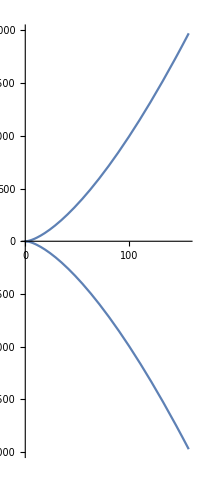

```mathematica
ParametricPlot[
{t^2,t (t^2-1)},
{t, -4π,4π}]
```

```mathematica
ParametricPlot3D[
{t^2,t (t^2-1), √(1-(t^2)^2-(t(t^2-1))^2)},
{t, -π,π}]
```

-Graphics3D-

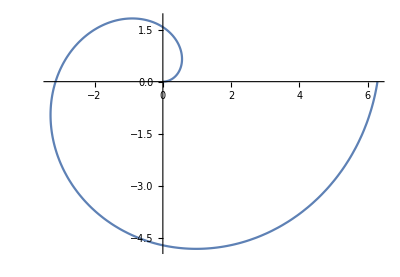

```mathematica
PolarPlot[θ,{θ,0,2π}]
```

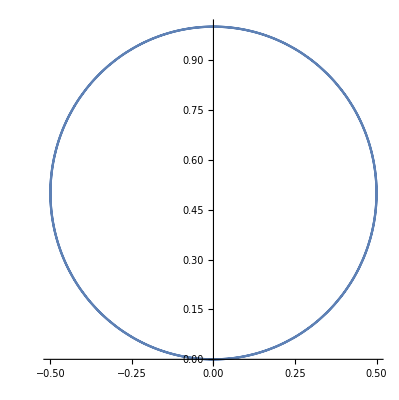

```mathematica
PolarPlot[Sin[θ],{θ,0,2π}]
```

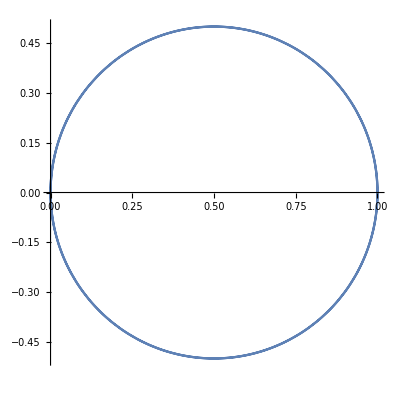

```mathematica
PolarPlot[Cos[θ],{θ,0,2π}]
```

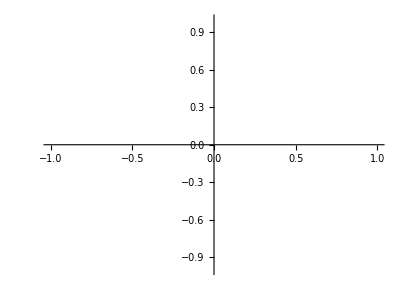

```mathematica
PolarPlot[Cos[θ]-Cos[θ],{θ,0,2π}]
```



```mathematica
PolarPlot[1,{θ,0,2π}]
```

```mathematica
ParametricPlot[{Cos[t], Sin[t]}, {t, 0, 2π}]
```

-Graphics-

```mathematica
ParametricPlot[{Cos[t], Sin[t]}, {t, 0, 2π}]
```

```mathematica
ParametricPlot[D[{Cos[t], Sin[t]},t], {t, 0, 2π}]
```

General::ivar: 0.000128228 is not a valid variable.

General::ivar: 0.128356 is not a valid variable.

-Graphics-

```mathematica
D[{Cos[t], Sin[t]},t]
```

{-Sin[t],Cos[t]}

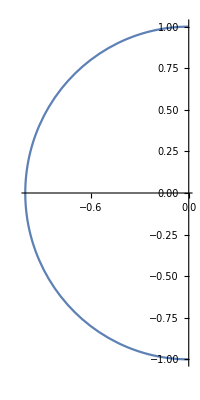

```mathematica
ParametricPlot[{-Sin[t],Cos[t]},{t,0,π}]
```

```mathematica
ParametricPlot[{Cos[t], Sin[t]}, {t, 0, 2π}]
```

```mathematica
{-Sin[t],Cos[t]}/.t->π/2
```

{-1,0}

```mathematica
Normalize[D[{Cos[t], Sin[t]},t]]
```

{-Sin[t]/(√(Abs[Cos[t]]^2+Abs[Sin[t]]^2)),Cos[t]/(√(Abs[Cos[t]]^2+Abs[Sin[t]]^2))}

```mathematica
FullSimplify[
Normalize[D[{Cos[t], Sin[t]},t]], Element[t, Reals]]
```

{-Sin[t],Cos[t]}

```mathematica
Normalize[{a,b}]=={a,b}
```

{a/(√(Abs[a]^2+Abs[b]^2)),b/(√(Abs[a]^2+Abs[b]^2))}=={a,b}

```mathematica
FullSimplify[
Normalize[{a,b}]=={a,b}, Element[a|b,Reals]]
```

{a/(√(a^2+b^2)),b/(√(a^2+b^2))}=={a,b}

```mathematica
Reduce[{a/(√(a^2+b^2)),b/(√(a^2+b^2))}=={a,b}]
```

a==-√(1-b^2)||a==√(1-b^2)

```mathematica
FindInstance[a==-√(1-b^2)||a==√(1-b^2),{a,b}]
```

{{a→-1/10 √(-451-240 ⅈ),b→-12/5-ⅈ/2}}

```mathematica
y== f'[a](x-a)+f[a]
```

y==f[a]+(-a+x) f'[a]

```mathematica
DSolve[y==f[a]+(-a+x) f'[a],{f[a]},{x,y}]
```

DSolve::dvnoarg: The function f[a] appears with no arguments.

DSolve[y==f[a]+(-a+x) f'[a],{f[a]},{x,y}]

```mathematica
With[{f={Cos[#],Sin[#]}&},
y== f'[a](x-a)+f[a]]
```

y=={Cos[a]-(-a+x) Sin[a],(-a+x) Cos[a]+Sin[a]}

```mathematica
With[{f={Cos[#],Sin[#]}&, a=π/2},
y== f'[a](x-a)+f[a]]
```

y=={π/2-x,1}

```mathematica
With[{f=Identity, a=1},
y== f'[a](x-a)+f[a]]
```

y==x

```mathematica
With[{f=Sin, a=π/4},
y== f'[a](x-a)+f[a]]
```

y==1/(√2)+(-π/4+x)/(√2)

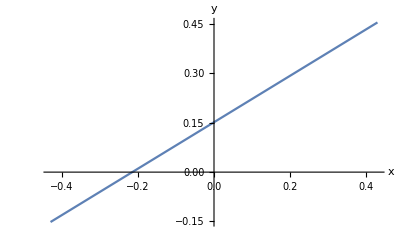

```mathematica
Plot[1/(√2)+(-π/4+x)/(√2),{x,-0.42920367320510344,0.42920367320510344},AxesLabel->{x,y}]
```

```mathematica
y== -(x-a)/f'[a]+f[a]
```

y==f[a]-(-a+x)/f'[a]

```mathematica
DSolve[y==f[a]-(-a+x)/f'[a],{f[a]},{x,y}]
```

DSolve::dvnoarg: The function f[a] appears with no arguments.

DSolve[y==f[a]-(-a+x)/f'[a],{f[a]},{x,y}]

```mathematica
With[{f=Identity, a=1},
y==f[a]-(-a+x)/f'[a]]
```

y==2-x

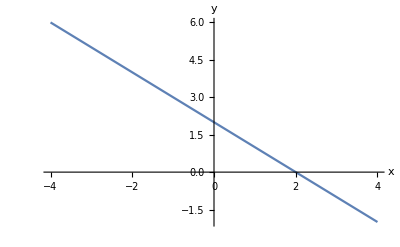

```mathematica
Plot[2-x,{x,-4.,4.},AxesLabel->{x,y}]
```

```mathematica
With[{f=Sin, a=1},
y==f[a]-(-a+x)/f'[a]]
```

y==-(-1+x) Sec[1]+Sin[1]

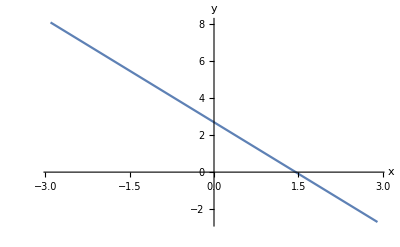

```mathematica
Plot[-(-1+x) Sec[1]+Sin[1],{x,-2.909297426825682,2.909297426825682},AxesLabel->{x,y}]
```

```mathematica
Manipulate[
Plot[{With[{f=Sin, a=b},
y==f[a]-(-a+x)/f'[a]], Sin[x]}, {x, b-π/2,b+π/2}, PlotRange->{-2, 2}], {b, 0, π/2}]
```

```mathematica
With[{f=Sin},
y==f[a]-(-a+x)/f'[a]]
```

y==-(-a+x) Sec[a]+Sin[a]

```mathematica
Manipulate[
Plot[
{-(-a+x) Sec[a]+Sin[a], Sin[x]},
 {x, a-π/2,a+π/2},
 PlotRange->{-2, 2}],
 {a, 0, π/2}]
```

```mathematica
With[{offset=2π},
Manipulate[
Plot[
{-(-a+x) Sec[a]+Sin[a], Sin[x]},
 {x, a-π/2,a+π/2},
 PlotRange->{-2, 2}],
{a, 0, offset}]]
```

```mathematica
With[{offset=2π},
Manipulate[
Show[{
Plot[
{-(-a+x) Sec[a]+Sin[a], Sin[x]},
 {x, a-π/2,a+π/2},
 PlotRange->{-2, 2}],
ListPlot[{{b, -(-b+a) Sec[b]+Sin[b]}}]
}],
{a,0,offset}, {b,-offset,offset}]]
```

```mathematica
With[{offset=2π},
Manipulate[
Show[{
Plot[
{-(-a+x) Sec[a]+Sin[a], Sin[x]},
 {x, a-π/2,a+π/2},
 PlotRange->{-2, 2}],
ListPlot[{{b, (-a+b) Sec[a]+Sin[a]}}]
}],
{a,0,offset}, {{b, 0},-offset,offset}]]
```

```mathematica
x
```

x

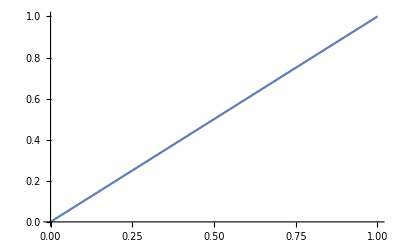

```mathematica
Plot[x, {x, 0, 1}]
```

```mathematica
Plot[x, {x, 0, 1}]
```

```mathematica
With[{f=Identity},
-(x-a)/f'[a]+f[a]]
```

2 a-x

```mathematica
Manipulate[Plot[2 a-x,{x,-2,2}],{a,-1,1}]
```

```mathematica
Manipulate[
Plot[{x, 2a-x}, {x, 0, 1}, PlotRange->{-1,1}],
{a, 0, 1}]
```

```mathematica
Manipulate[
Plot[{x, 2a-x},
{x, 0, 1},
PlotRange->{-1,1}],
{a, 0, 1}]
```

```mathematica
Manipulate[
Show[{
Plot[{x, 2a-x},
{x, 0, 1},
PlotRange->{-1,1}],
ListPlot[{{b, 2a-b}}]
}],
{a, 0, 1}, {b, -1, 1}]
```

```mathematica
Manipulate[
Show[{
Plot[{x, 2a-x},
{x, 0, 1},
PlotRange->{-1,1}],
ListPlot[{{b, 2a-b}}]
}],
{a, 0, 1}, {b, -1, 1}]
```

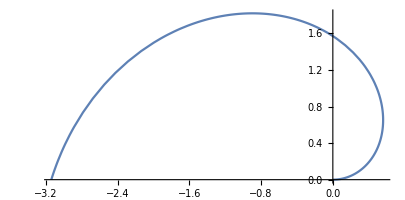

```mathematica
PolarPlot[θ, {θ, 0, π}]
```

```mathematica
PolarPlot[θ, {θ, 0, 2π}]
```

-Graphics-

```mathematica
Manipulate[
Show[{
Plot[{x, 2a-x},
{x, 0, 1},
PlotRange->{-2,2}],
ListPlot[{{b, 2a-b}}]
}],
{a, 0, 1}, {{b,0}, -1, 1}]
```

```mathematica
Manipulate[
Show[{
Plot[{x, 2a-x},
{x, 0, 1},
PlotRange->{-2,2}],
ListPlot[{{a-b, 2a-b}}]
}],
{{a,1/2}, 0, 1}, {{b,0}, -1, 1}]
```

```mathematica
Manipulate[
Show[{
Plot[{x, 2a-x},
{x, 0, 1},
PlotRange->{-2,2}],
ListPlot[{{a-b,- 2a+b}}]
}],
{{a,1/2}, 0, 1}, {{b,0}, -1, 1}]
```

```mathematica
Manipulate[
Show[{
Plot[{x, 2a-x},
{x, 0, 1},
PlotRange->{-2,2}],
ListPlot[{{a-b,2a+b}}]
}],
{{a,1/2}, 0, 1}, {{b,0}, -1, 1}]
```

```mathematica
Manipulate[
Show[{
Plot[{x, 2a-x},
{x, 0, 1},
PlotRange->{-2,2}],
ListPlot[{{a-b,2a+b}}]
}],
{{a,1/2}, 0, 1}, {{b,0}, -1, 1}]
```

```mathematica
Manipulate[
Show[{
Plot[{x, 2a-x},
{x, 0, 1},
PlotRange->{-2,2}],
ListPlot[{{a-b,2a+b}}]
}],
{{a,1/2}, 0, 1}, {{b,0}, -1, 1}]
```